# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order2_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles[[1]]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse2\1) Fitting Scale\Export

# Parametrization of the Lobe’s Flattening Factor σ_n

```mathematica
paramsFlat = Table[Table[rawFiles[[albedo]][[j]][[i]][[4]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsFlat[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsFlat[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsFlat[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Green],
ListPlot3D[paramsFlat[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Yellow]
 ]
```

-Graphics3D-

We see that for most albedo values, the shape is very similar and there is no dependency on the albedo at all, which is good (only the global scale factor σ should be dependent on albed).
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in α is from index 1 to about 9.
There is also a slight inflection of the curve for grazing angles indicating a slight dependency on θ.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

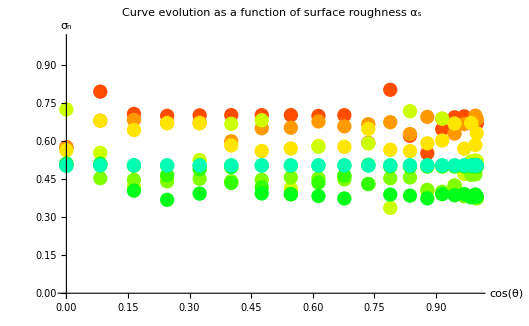

```mathematica
paramsFlat0=paramsFlat[[1]]; (* We only work on albedo = 1 *)
parmsFlatCurves= Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,9}];
Show[Table[ListPlot[parmsFlatCurves[[j]],PlotRange->{0,1},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ_n"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,9}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0.637228 | b→0.691733 | c→-1.56796 | d→0.916318
a→0.61392 | b→0.362812 | c→-0.772275 | d→0.480068
a→0.606117 | b→0.418549 | c→-1.29455 | d→0.90567
a→0.64103 | b→-0.787361 | c→1.57823 | d→-0.934087
a→0.490621 | b→-0.29364 | c→0.585379 | d→-0.368055
a→0.530887 | b→-0.372304 | c→0.411102 | d→-0.057822
a→0.509533 | b→-0.607114 | c→1.10629 | d→-0.632512
a→0.508738 | b→-0.0293586 | c→0.0514455 | d→-0.0271078
a→0.503479 | b→0.00722808 | c→-0.0132032 | d→0.00716663)

Now let’s try and fit the individual parameters using another fitting for each one:

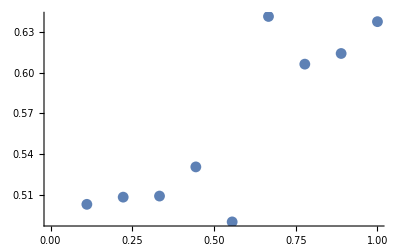

```mathematica
paramsFlatA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatA]
ListPlot[paramsFlatB];
ListPlot[paramsFlatC];
ListPlot[paramsFlatD];
```

Parameter A is the most stable so let’s start with that one...

0.548306-0.469563 α+1.23569 α^2-0.68155 α^3

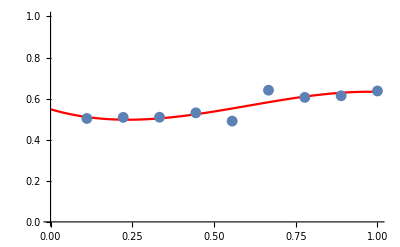

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsFlatA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1}],
ListPlot[paramsFlatA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0.721166 | c→-1.62207 | d→0.945665
a→0. | b→0.263342 | c→-0.589384 | d→0.380886
a→0. | b→0.392672 | c→-1.24697 | d→0.879868
a→0. | b→-0.39071 | c→0.848923 | d→-0.538584
a→0. | b→-0.709473 | c→1.34995 | d→-0.782684
a→0. | b→-0.324697 | c→0.32357 | d→-0.0103534
a→0. | b→-0.568527 | c→1.03535 | d→-0.594037
a→0. | b→0.0468171 | c→-0.088615 | d→0.0488474
a→0. | b→-0.0400445 | c→0.0737145 | d→-0.039969)

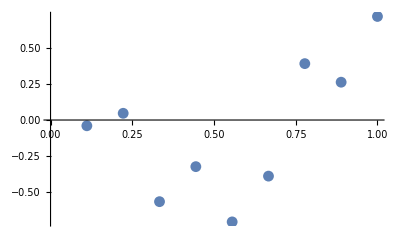

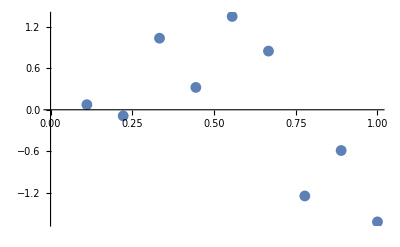

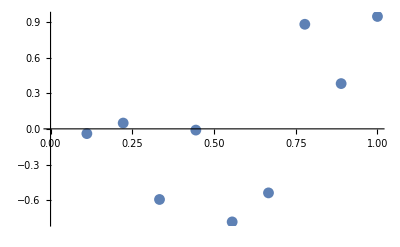

```mathematica
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatB->{0,1}]
ListPlot[paramsFlatC->{-1,0}]
ListPlot[paramsFlatD->{0,1}]
```

We see the model is behaving a little bit better now so we can proceed and fit the next coefficients:

-0.530284+0.83262 α

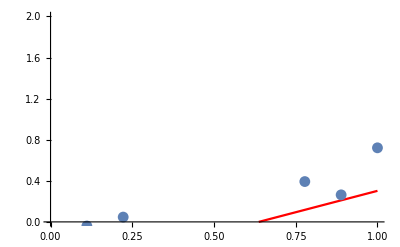

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+0*c*u^2+0*d*u^3;
fittingB = FindFit[ paramsFlatB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{0,2}],
ListPlot[paramsFlatB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-5.55112×10^-16 | c→-0.462293 | d→0.189447
a→0. | b→-4.44089×10^-16 | c→-0.441185 | d→0.284254
a→0. | b→-4.44089×10^-16 | c→-0.484464 | d→0.382686
a→0. | b→-4.44089×10^-16 | c→-0.301653 | d→0.211632
a→0. | b→-8.88178×10^-16 | c→-0.427136 | d→0.37604
a→0. | b→-2.77556×10^-16 | c→-0.131854 | d→0.286599
a→0. | b→1.66533×10^-16 | c→0.160909 | d→-0.0238744
a→0. | b→1.33227×10^-15 | c→0.997078 | d→-0.659063
a→0. | b→1.55431×10^-15 | c→1.17506 | d→-0.758084)

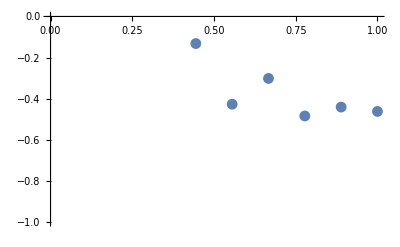

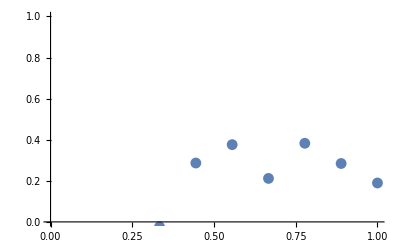

```mathematica
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatC,PlotRange->{-1,0}]
ListPlot[paramsFlatD,PlotRange->{0,1}]
```

The model is continuing to improve in stability, let’s keep on replacing...

1.87671-5.97366 α+3.71245 α^2

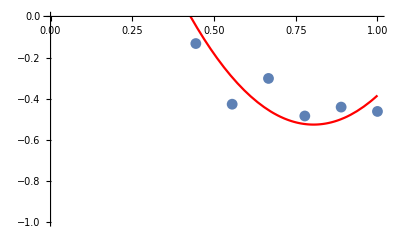

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+0*d*u^3;
fittingC = FindFit[ paramsFlatC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-1,0}],
ListPlot[paramsFlatC]
]
```

#### Replacing C and Fitting D

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→0.10544
a→0. | b→0. | c→0. | d→0.347664
a→0. | b→0. | c→0. | d→0.42501
a→0. | b→0. | c→0. | d→0.378019
a→0. | b→0. | c→0. | d→0.234622
a→0. | b→0. | c→0. | d→0.192732
a→0. | b→0. | c→0. | d→-0.171889
a→0. | b→0. | c→0. | d→-0.373446
a→0. | b→0. | c→0. | d→-0.848513)

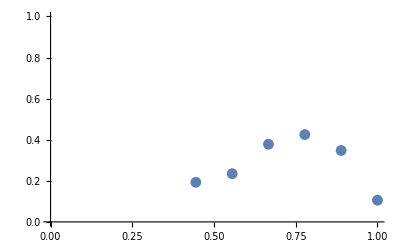

```mathematica
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatD,PlotRange->{0,1}]
```

-0.581004+1.10373 α

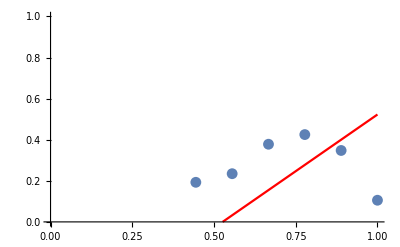

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+0*c*u^2+0*d*u^3;
fittingD = FindFit[ paramsFlatD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1}],
ListPlot[paramsFlatD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.913643-1.65548 α+1.39617 α^2-0.320331 α^3
	b(α_s)= 0.0447239+0.62474 α
	c(α_s)= -0.118844-0.973213 α+0.36902 α^2
	d(α_s)=0.132577+0.16975 α
	
	σ_n(μ,α_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ]
fA[α_]= 0.9136434030473861-1.6554846256054254 α+1.396170391613371 α^2-0.3203305249468263 α^3;
fB[α_]= 0.044723925680673265+0.6247396225423497 α;
fC[α_]= -0.11884367470512597-0.973212684779483 α+0.36902017638601514 α^2;
fD[α_]=0.13257717032932556+0.1697498085943817 α;
(*fA[α_]= 0.8846422855624879-1.405547722190124 α+0.8622861833686603 α^2;
fB[α_]= 1.3711661211982282-8.51539991518015 α+5.496099699231776 α^2;
fC[α_]= 7.753321114389069-8.10901036151992 α+5.808056815711743 α^2;
fD[α_]=-3.187108490510769-0.2936373719156488 α;*)
fFlat[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
fFlat[0.99691733373312797619777340874204,0.3333]

Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];
Plot3D[fFlat[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ_n"},PlotLabel->"Lobe flattening factor",PlotRange->{0,1}]
```

0.544944

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fFlat[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

# Parametrization of the lobe’s Scale factor σ

```mathematica
paramsScale = Table[Table[rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScale[[albedo]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,resZ}]
]
```

-Graphics3D-

So it appears the scale factor σ is also quite smooth and should be fitted in the same way as the flattening factor σ_n.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

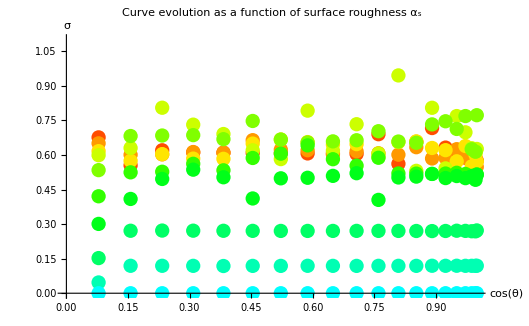

```mathematica
paramsScale0=paramsScale[[1]]; (* We only work on albedo = 1 *)
parmsScaleCurves= Table[Table[{Cos[(i-1)/resX*π/2],paramsScale0[[j]][[i]]},{i,1,resX}],{j,1,resY}];
Show[Table[ListPlot[parmsScaleCurves[[j]],PlotRange->{0,1.1},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,resY}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0.711776 | b→-0.874302 | c→1.91361 | d→-1.16555
a→0.654331 | b→-0.315573 | c→0.75978 | d→-0.532914
a→0.62199 | b→-0.334968 | c→1.11802 | d→-0.826223
a→0.625026 | b→0.251366 | c→-0.177239 | d→-0.0435017
a→0.49939 | b→1.14034 | c→-2.07019 | d→1.14636
a→0.355951 | b→1.08943 | c→-1.52654 | d→0.58678
a→0.225821 | b→1.51566 | c→-2.59634 | d→1.37299
a→0.129747 | b→0.831523 | c→-1.41853 | d→0.733851
a→0.0332894 | b→0.500591 | c→-0.850969 | d→0.439984
a→1.×10^-6 | b→3.88489×10^-23 | c→-9.38603×10^-22 | d→-3.3039×10^-22)

Now let’s try and fit the individual parameters using another fitting for each one:

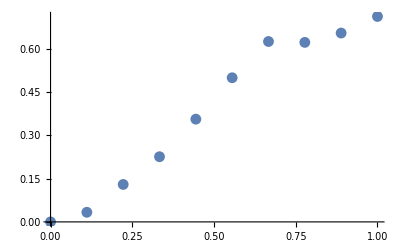

```mathematica
paramsScaleA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleA]
ListPlot[paramsScaleB];
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

All curves seem to behave the same way so let’s simply start with coefficient a:

-0.0107523+0.309192 α+1.81942 α^2-1.43381 α^3

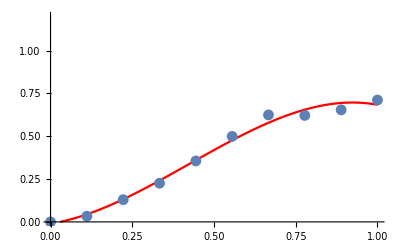

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsScaleA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1.2}],
ListPlot[paramsScaleA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-0.686029 | c→1.56707 | d→-0.977479
a→0. | b→-0.589429 | c→1.26385 | d→-0.806477
a→0. | b→-0.564307 | c→1.54015 | d→-1.05532
a→0. | b→0.562792 | c→-0.750468 | d→0.267591
a→0. | b→1.29433 | c→-2.35363 | d→1.30018
a→0. | b→1.06069 | c→-1.47363 | d→0.558068
a→0. | b→1.41007 | c→-2.40198 | d→1.26751
a→0. | b→0.815738 | c→-1.38948 | d→0.718084
a→0. | b→0.427176 | c→-0.715836 | d→0.366647
a→0. | b→0.0730427 | c→-0.134447 | d→0.0729646)

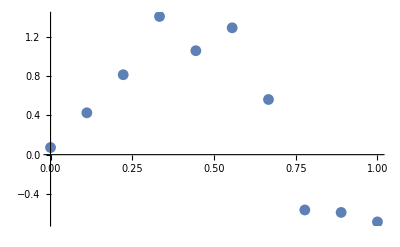

```mathematica
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleB]
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

-0.143525+9.10964 α-17.5061 α^2+7.66315 α^3

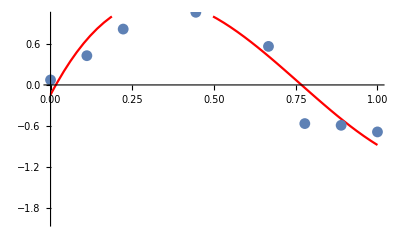

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+c*u^2+d*u^3;
fittingB = FindFit[ paramsScaleB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{-2,1}],
ListPlot[paramsScaleB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-2.66454×10^-15 | c→2.09544 | d→-1.32207
a→0. | b→-1.11022×10^-15 | c→1.00493 | d→-0.637609
a→0. | b→-8.32667×10^-17 | c→0.0956411 | d→-0.113236
a→0. | b→2.22045×10^-16 | c→-0.354032 | d→0.00904335
a→0. | b→8.88178×10^-16 | c→-1.06277 | d→0.458312
a→0. | b→2.22045×10^-15 | c→-1.63785 | d→0.665165
a→0. | b→1.77636×10^-15 | c→-1.90801 | d→0.945347
a→0. | b→2.66454×10^-15 | c→-2.17801 | d→1.23235
a→0. | b→8.88178×10^-16 | c→-1.36912 | d→0.792709
a→0. | b→-6.66134×10^-16 | c→0.465381 | d→-0.318231)

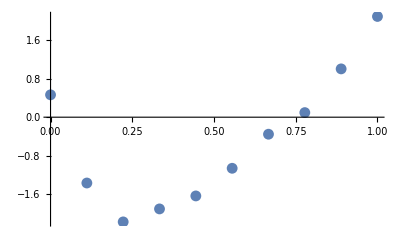

```mathematica
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleC]
ListPlot[paramsScaleD];
```

0.255088-15.927 α+31.6456 α^2-14.0796 α^3

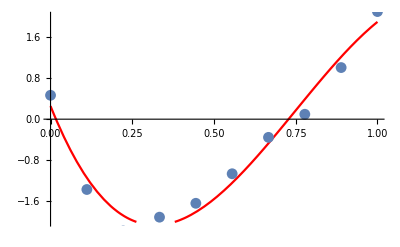

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+d*u^3;
fittingC = FindFit[ paramsScaleC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-2,2}],
ListPlot[paramsScaleC]
]
```

#### Replacing C and Fitting the D Coefficient

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→-1.1046
a→0. | b→0. | c→0. | d→-0.862499
a→0. | b→0. | c→0. | d→-0.427399
a→0. | b→0. | c→0. | d→0.134215
a→0. | b→0. | c→0. | d→0.650028
a→0. | b→0. | c→0. | d→0.84965
a→0. | b→0. | c→0. | d→1.10864
a→0. | b→0. | c→0. | d→0.906147
a→0. | b→0. | c→0. | d→0.548692
a→0. | b→0. | c→0. | d→-0.0910963)

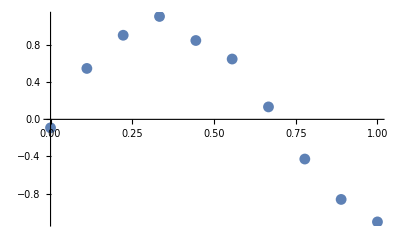

```mathematica
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleD]
```

-0.138572+8.5056 α-17.5193 α^2+7.99609 α^3

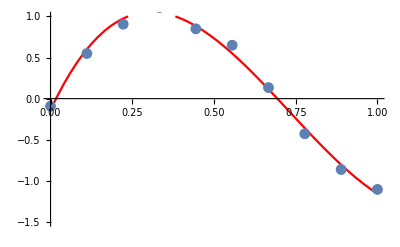

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+c*u^2+d*u^3;
fittingD = FindFit[ paramsScaleD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{-1.5,1}],
ListPlot[paramsScaleD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3
	b(α_s)= -0.10099+7.22596 α-19.4905 α^2+10.7698 α^3
	c(α_s)= 0.139826-11.4291 α+30.1773 α^2-16.7894 α^3
	d(α_s)=-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3
	
	σ(μ,σ_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ,fA,fB,fC,fD]
fA[α_]= 0.016673375075225604-0.525209545615772 α+5.24220269537287 α^2-3.5690085024568186 α^3
fB[α_]= -0.10099003574844712+7.225961805352702 α-19.49049342659228 α^2+10.769848952215131 α^3
fC[α_]= 0.13982571795990942-11.429145510606348 α+30.177292378971725 α^2-16.789426306986503 α^3
fD[α_]=-0.065024475640786+5.731247014927747 α-14.997450899818153 α^2+8.3291032822247 α^3
fScale[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];
Plot3D[fScale[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ"},PlotLabel->"Lobe Scale factor",PlotRange->{0,1.2}]
```

(0.139826-11.4291 α+30.1773 α^2-16.7894 α^3) (0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3) (-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3) (-0.10099+7.22596 α-19.4905 α^2+10.7698 α^3)

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsScale0,PlotRange->{0,1.1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fScale[Cos[(i-1)/resX π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Great!
Now we only need to find the dependence between the scale and the albedo...

# Dependence of Scale σ on albedo ρ

We try to fit our scale model to all albedo using the “amp” free coefficient to see how the amplitude is related to ρ:

```mathematica
paramsScaleMuAlpha = Table[
	Table[
		{ Cos[Mod[i,resX]/resX*π/2], 1-Quotient[i,resX]/(resY-1),paramsScale[[albedo]][[1+Quotient[i,resX]]][[1+Mod[i,resX]]]},{i,0,resX*resY-1}]
, {albedo,1,resZ}];
paramsScaleMuAlpha[[1]];
ListPlot3D[paramsScaleMuAlpha[[1]]];
```

{{amp→0.873637},{amp→0.823553},{amp→0.567221},{amp→0.411798},{amp→0.247404},{amp→0.137639},{amp→0.0299138},{amp→0.00711995}}

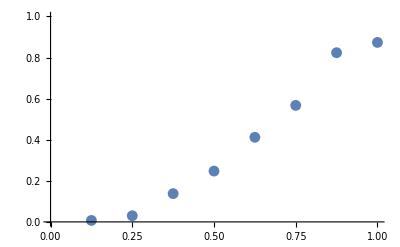

```mathematica
modelRho=amp * fScale[μ,α];
fittingRho = Table[FindFit[ paramsScaleMuAlpha[[albedo]],{modelRho},{amp},{μ,α} ],{albedo,1,resZ}]
listAmps=Table[{1-(albedo-1)/resZ, amp/.fittingRho[[albedo]]},{albedo,1,resZ}];
ListPlot[listAmps,PlotRange->{0,1}]
```

{a→0.,b→0.0884837,c→0.860712}

0.0884837 ρ+0.860712 ρ^2

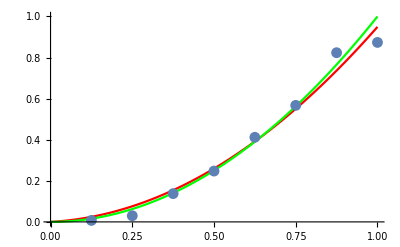

```mathematica
modelAmp=0*a+b*u+c*u^2;
fittingAmp=FindFit[listAmps,modelAmp,{a,b,c},u]
fAmp[ρ_]=Evaluate[modelAmp/.fittingAmp/.u->ρ]
fAmp2[ρ_]=ρ^2;
Show[
Plot[fAmp[ρ],{ρ,0,1},PlotStyle->Red,PlotRange->{0,1}],
Plot[fAmp2[ρ],{ρ,0,1},PlotStyle->Green,PlotRange->{0,1}],
ListPlot[listAmps]
]
```

Final Expression

We obtain the final expression for the scale parameter σ :

	a(α_s)= 0.0166734-0.52521 α+5.2422 α^2-3.56901 α^3
	b(α_s)= -0.10099+7.22596 α-19.4905 α^2+10.7698 α^3
	c(α_s)= 0.139826-11.4291 α+30.1773 α^2-16.7894 α^3
	d(α_s)=-0.0650245+5.73125 α-14.9975 α^2+8.3291 α^3
	
	σ(μ,σ_s, ρ) = ρ^2 [ a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3]

```mathematica
fScale2[μ_,α_,ρ_] = ρ^2 * fScale[μ,α];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScaleMuAlpha[[albedo]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,6}],
Table[Plot3D[fScale2[μ,α,1-(albedo-1)/resZ],{μ,0,1},{α,0,1},{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->Red],{albedo,1,6}]
]
```

-Graphics3D-

And we’re done with a very good match for scale!